```mathematica
(*初始化删除变量及设定目录*)
ClearAll["Global`*"];
SetDirectory[NotebookDirectory[]];
jointn=2;
```

```mathematica
(*初始化*)
RotX[x_]:={{1,0,0,0},{0,Cos[x],-Sin[x],0},{0,Sin[x],Cos[x],0},{0,0,0,1}}
RotY[x_]:={{Cos[x],0,Sin[x],0},{0,1,0,0},{-Sin[x],0,Cos[x],0},{0,0,0,1}}
RotZ[x_]:={{Cos[x],-Sin[x],0,0},{Sin[x],Cos[x],0,0},{0,0,1,0},{0,0,0,1}}
TransX[x_] :={{1,0,0,x},{0,1,0,0},{0,0,1,0},{0,0,0,1}}
TransY[x_] :={{1,0,0,0},{0,1,0,x},{0,0,1,0},{0,0,0,1}}
TransZ[x_] :={{1,0,0,0},{0,1,0,0},{0,0,1,x},{0,0,0,1}}
iTi[a_,α_,d_,θ_]:=TransX[a].RotX[α].TransZ[d].RotZ[θ]
```

```mathematica
(*设定变量*)
Q=Table[Subscript[q, i][t],{i,jointn}];
dQ=D[Q,t];
Subscript[T0, 1]=iTi[0,0,0,Q[[1]]];
Subscript[T0, 2]=Subscript[T0, 1].iTi[l1,Q[[2]]+Pi/2,0,0];
Subscript[T0, 3]=Subscript[T0, 2].TransY[l2];
T0=Table[Subscript[T0, i],{i,3}];
in=m l2^2/3;(*摆转动惯量I*)

(*设定参数*)
parameter={M->1.096,m->0.109,l2->0.25,g->-9.8,l1->0.2};
```

```mathematica
(*建模*)
j0={0,0,0,1};

jp=Table[T0[[i]].j0,{i,3}];

Graphics3D[{
Thick,Line[Table[jp[[i,1;;3]],{i,3}](*,T0[[1,1;;3]].j0,T0[[2,1;;3]].j0*)],
Blue,Sphere[j0[[1;;3]],0.008],
Red,Sphere[Table[jp[[i,1;;3]],{i,jointn}],0.005],
Opacity[.3],Sphere[jp[[3,1;;3]],0.01]
},Axes->True,AxesLabel->{x,y,z}]/.{Subscript[q, 1][t]->30 Pi/180,Subscript[q, 2][t]->0 Pi/180}~Join~parameter
```

-Graphics3D-

```mathematica
(*一阶倒立摆微分方程*)
x[t]=Subscript[q, 1][t]l1/.parameter;
θ[t]=Subscript[q, 2][t]/.parameter;
dx=D[x[t],t];
dθ=D[θ[t] ,t];
ddx=D[x[t],{t,2}];
ddθ=D[θ[t] ,{t,2}];
equ={
ddx==(m^2 g l2^2/(in(M+m)+M m l2^2)) θ[t]+((in+m l2^2)/(in(M+m)+M m l2^2)) τ,
ddθ==(m g l2(M+m)/(in(M+m)+M m l2^2))θ[t]+(m l2/(in(M+m)+M m l2^2))τ
}/.parameter;
```

```mathematica
(*PID控制器*)
Kp=8 10^-1;
Kv=4 10^-1;
xd=0;(*目标位移*)
dxd=0 10^-5;(*目标速度*)
(*输入力矩*)
τ=pid=(M )(ddx+Kv(dxd-dx)+Kp(xd-x[t]))/.parameter;
```

```mathematica
(*模拟时长*)
finishtime=4.5;(*The simulation time from 0 to the finishtime*)
(*初始条件设定*)
initial={Subscript[q, 1][0]==0,Subscript[q, 2][0]==45Pi/180,Subscript[q, 1]'[0]==0,Subscript[q, 2]'[0]==0};
Monitor[
data=NDSolve[{equ,initial},Q,{t,0,finishtime},SolveDelayed -> True,EvaluationMonitor:>(indicatortime=t;)],
"t="Dynamic[indicatortime,UpdateInterval->1]];
```

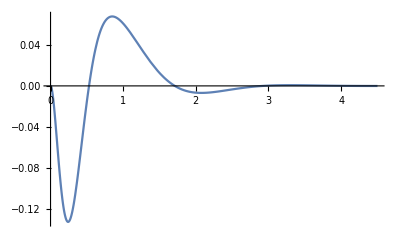

```mathematica
(*小车位移图*)
Plot[Evaluate[x[t] /.data],{t,0,finishtime},PlotRange->All,PlotLegends->"x[t]"]
```

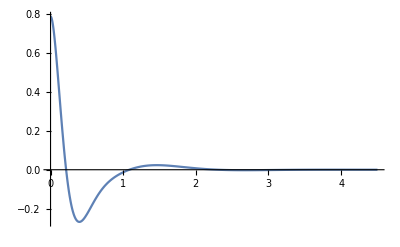

```mathematica
(*杆角度变化*)
Plot[Evaluate[θ[t]/.data],{t,0,finishtime},PlotRange->All,PlotLegends->"θ[t]"]
```

```mathematica
(*动画*)
frame=Table[
Graphics3D[{
Thick,Line[Table[jp[[i,1;;3]],{i,3}]],
Blue,Sphere[j0[[1;;3]],0.03],
Red,Sphere[Table[jp[[i,1;;3]],{i,jointn}],0.02],
Opacity[.3],Green,Sphere[jp[[3,1;;3]],0.015]
},Axes->True,AxesLabel->{x,y,z},PlotRange->{{-.5,.5},{-.5,.5},{-.4,.4}}
]/.parameter~Join~First@data,{t,0,finishtime,finishtime/120}];
```

```mathematica
ListAnimate[frame,24,AnimationRunning->True]
```

```mathematica
(*动画输出至当前目录下*)
If[False,Export["Simulation"<>DateString["ISODate"]<>".gif",frame,"DisplayDurations"->0.05]]
```

Simulation2019-07-13.gif